```mathematica
Clear["Global`*"]
notation ={wa->Subscript[ω, a],wo->Subscript[ω, 0],wp->Subscript[ω, p],deltaA->Subscript[Δ, a],deltaO->Subscript[Δ, 0], cb ->Subscript[c, b] ,ca ->Subscript[c, a],
uab->Subscript[μ, ab],uba->Subscript[μ, ba],  eps ->ℰ, cbnp1 -> Subscript[c,b,n+1], cn0 -> Subscript[c, n0]};
```

Section A
Resonance for strong coupling g>>(Κ,γ)

Setting up driven atom-cavity Hamiltonian with coupling in |n,g>, |n-1,e> basis and solving for energy eigenvalues:

```mathematica
H = {{n*wa,g*Sqrt[n]},{g*Sqrt[n],wo+(n-1)*wa}};
MatrixForm[H] /. notation
En=Eigenvalues[H]//Simplify;
En /. notation
Eminus = En[[1]];
Eplus = En[[2]];
Epm = 1/2 ((-1+2 n) wa + PlusMinus[√(4 g^2 n+(wa-wo)^2)]+wo) ;
```

(n ω_a | g √n
g √n | ω_0+(-1+n) ω_a)

{1/2 (ω_0+(-1+2 n) ω_a-√(4 g^2 n+(-ω_0+ω_a)^2)),1/2 (ω_0+(-1+2 n) ω_a+√(4 g^2 n+(-ω_0+ω_a)^2))}

Case for same detuning Δ_0=Δ_a
Then ω_0=ω_a. The eigenvalues simplify to:

```mathematica
Epmsame = Epm /. wo -> wa;
Epmsame /.notation
```

1/2 (±(2 √(g^2 n))+ω_a+(-1+2 n) ω_a)

First consider n=1.
For resonance, the photon energy must be equal to the excited state transition energy, ω_p=E_(1,±).

```mathematica
Clear[wp]
eq = Thread[wp == Epmsame] /. n->1;
eq  /.notation//Simplify
```

±(2 √(g^2))+2 ω_a==2 ω_p

Subtracting 2 ω_p from both sides in order to write the equation in terms of detuning, (and dividing both sides by 2)

```mathematica
eq = Thread[ wa+±(√(g^2))-wp==0] /. wa -> deltaA + wp //Simplify ;
eq /.notation
```

±√(g^2)+Δ_a==0

Finally, solve for detuning needed for n=1 resonance:

```mathematica
Solve[eq, deltaA]//FullSimplify
```

{{deltaA→-±√(g^2)}}

Thus for equal detuning, the resonance condition of the 1-photon state is that Δ_0=Δ_a = ±g.
Now consider n=2 for resonance of the 2-photon state. Want 2ω_p=E_(2,±) to be satisfied.

```mathematica
Clear[wp]
eq = Thread[2wp == Epmsame] /. n->2;
eq  /.notation//Simplify
```

±(2 √2 √(g^2))+4 ω_a==4 ω_p

```mathematica
eq = Thread[ 2wa+±(√2  √(g^2))-2wp==0] /. wa -> deltaA + wp //Simplify ;
eq /.notation
```

±(√2 √(g^2))+2 Δ_a==0

Assume that 1-photon state is already resonant ie Δ_0=Δ_a = ±g

```mathematica
eq /. deltaA ->PlusMinus[g]
```

2 (±g)+±(√2 √(g^2))==0

Simplifying by hand, the expression becomes (2 ±√2) g=0,  which is impossible unless g=0. Thus, the 2-photon state cannot be resonant when the 1-photon state is already resonant, even with losses, since (2 ±√2) g >> (Κ,γ) with strong coupling. 

Independent detunings Δ_0≠Δ_a
Now relaxing the constraint that the detunings must be equal,

```mathematica
Epmdiff = Epm ;
```

Look at n=1 case:

```mathematica
Clear[wp,wa,wo]
eq = Thread[wp == Epmdiff] /. n->1;
eq  /.notation//Simplify
```

±√(4 g^2+(ω_0-ω_a)^2)+ω_0+ω_a==2 ω_p

Subtracting 2wp from both sides and rewriting by hand:

```mathematica
eq = Thread[wa+wo-2wp+±√(4 g^2+(wa-wo)^2)==0];
eq /.notation
```

±√(4 g^2+(-ω_0+ω_a)^2)+ω_0+ω_a-2 ω_p==0

Rewrite in terms of detuning. Note that ω_a- ω_0= (ω_a-ω_p)-(ω_0-ω_p) = Δ_a-Δ_0

```mathematica
eqdet = eq /. {wa ->deltaA + wp, wo -> deltaO + wp};
eqdet /.notation
```

±√(4 g^2+(-Δ_0+Δ_a)^2)+Δ_0+Δ_a==0

Moving right-hand detuning terms to RHS, squaring both sides of the equation, and simplifying gives the resulting constraint relation for the detunings:

```mathematica
eqdet = Thread[(deltaA-deltaO)^2+4 g^2==(deltaA+deltaO)^2];
eqdet /.notation
eqdet /.notation//FullSimplify
```

4 g^2+(-Δ_0+Δ_a)^2==(Δ_0+Δ_a)^2

g^2==Δ_0 Δ_a

Thus for n=1 resonance, must have g^2==Δ_0 Δ_a. Note that the equation requires the detunings to have the same sign (both positive or both negative). For equal detunings, matches condition previously derived ie Δ_0=Δ_a=±g 

As before, consider n=2, resonance of 2-photon state with relaxed detuning condition.

```mathematica
Clear[wp,wa,wo]
eq = Thread[2wp == Epmdiff] /. n->2;
eq  /.notation//Simplify
```

±√(8 g^2+(ω_0-ω_a)^2)+ω_0+3 ω_a==4 ω_p

```mathematica
eqdet = eq /. {wa ->deltaA + wp, wo -> deltaO + wp};
eqdet /.notation //Simplify
```

±√(8 g^2+(Δ_0-Δ_a)^2)+Δ_0+3 Δ_a==0

Substitute 1-photon resonance condition:

```mathematica
eqdetres= eqdet /. {g^2 ->deltaA *deltaO};
eqdetres /.notation //Simplify
```

±√(Δ_0^2+6 Δ_0 Δ_a+Δ_a^2)+Δ_0+3 Δ_a==0

Again, the equation is not possible for any detunings ie ±√(Δ_0^2+6 Δ_0 Δ_a+Δ_a^2)==-(Δ_0+3 Δ_a)is not true. Thus for independent atom and cavity detunings, the transition to the 2-photon state is off resonance when the 1-photon state is resonant.

Plotting log g^(2)(0) as a function of cavity detuning, for constant atom detunings.

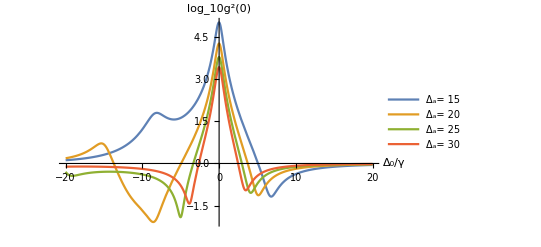

```mathematica
k=1; gamma=k; eps = 0.01; g=10;
dap = da -I*k/2;
dop = do - I*gamma/2;
C1g=(eps*dop)/(g^2-dap*dop);
C2g=(eps^2*((dap+dop)*dop+g^2))/(Sqrt[2]*(dap*dop-g^2)*((dap+dop)*dap-g^2));
g2=(2*Abs[C2g]^2)/Abs[C1g]^4;
lg2=Log10[g2];
Plot[{lg2/.da->15,lg2/.da->20,lg2/.da->25,lg2/.da->30},{do,-20,20},PlotRange->All,PlotLegends->{"Δ_a= 15 ","Δ_a= 20 ","Δ_a= 25 ","Δ_a= 30 "},AxesLabel->{"Δ_0/γ","log_10g^2(0)"}]
```

Section B
Coefficients for g2(0) correlation function with weak coupling g~(Κ,γ)

```mathematica
Psi = {c0g[t], c1g[t],c0e[t],c2g[t],c1e[t]}; 
MatrixForm[Psi]
```

(c0g[t]
c1g[t]
c0e[t]
c2g[t]
c1e[t])

```mathematica
lhs = D[Psi, t];

eqlist1= Thread[rhs == lhs]; MatrixForm[eqlist1] /. notation
```

(rhs==c0g'[t]
rhs==c1g'[t]
rhs==c0e'[t]
rhs==c2g'[t]
rhs==c1e'[t])